```mathematica
ContourPlot3D[SphericalHarmonicY[1,1,{x,-100,100},{y,-100,100},{z,-100,100}]
```

-Graphics3D-

```mathematica
Export
```

```mathematica
SphericalPlot3D[Abs[SphericalHarmonicY[1,0,θ,ψ]],{θ,-π,π},{ψ,-π,π},PlotRange->All]
```

-Graphics3D-

```mathematica
s[x_,y_,z_]:=Exp[-(x^2+y^2+z^2)]
```

```mathematica
r=ImplicitRegion[s[x,y,z]+x s[x,y,z]+y s[x,y,z]+z s[x,y,z]==0.5,{x,y,z}];
RegionPlot3D[r]
```

-Graphics3D-

```mathematica
ContourPlot3D[z s[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1},Contours->{{.4,Red},{-.4,Blue}},PlotPoints->5]
```

-Graphics3D-

```mathematica
graphs=Table[ContourPlot3D[z s[x+2-t/10,y,z]-z s[x-2+t/10,y,z],{x,-4.,4.},{y,-4.,4.},{z,-4.,4.},Contours->{{.05,Red},{-.05,Blue}},PlotPoints->5],{t,0,10}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ContourPlot3D[z s[x+2Cos[π/3],y+2Sin[π/3],z]+z s[x+2Cos[π/3],y-2Sin[π/3],z]+ z s[x,y,z],{x,-4.,4.},{y,-4.,4.},{z,-4.,4.},Contours->{{.1,Red},{-.1,Blue}}]
```

```mathematica
ContourPlot3D[Sum[z s[x+2Cos[n π/3],y+2Sin[n π/3],z],{n,1,6}],{x,-4.,4.},{y,-4.,4.},{z,-4.,4.},Contours->{{.1,Directive[Red,Opacity[0.7]]},{-.1,Directive[Blue,Opacity[0.7]]}},MaxRecursion->1,PlotPoints->5,Mesh->None]
```

-Graphics3D-

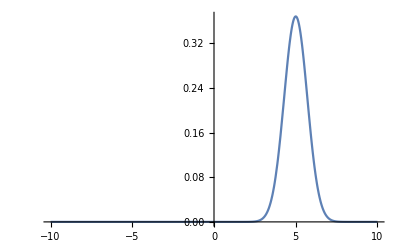

```mathematica
Plot[(z s[x+5Cos[π/3],y+5Sin[π/3],z]+z s[x+5Cos[π/3],y-5Sin[π/3],z]+ z s[x-5,y,z])/.{z->1,y->0},{x,-10,10},PlotRange->All]
```

```mathematica
ListAnimate[graphs]
```

```mathematica
px=ContourPlot3D[s[x,y,z]+x s[x,y,z]+y s[x,y,z]+z s[x,y,z],{x,-3.,3.},{y,-3.,3.},{z,-3.,3.},Contours->{{.04,Red},{-.04,Blue}},PlotPoints->5]
```

-Graphics3D-

```mathematica
Solve[s[x,y,z]+x s[x,y,z]+y s[x,y,z]+z s[x,y,z]==1/2,{x,y,z}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^(-x^2-y^2-z^2)+ⅇ^(-x^2-y^2-z^2) x+ⅇ^(-x^2-y^2-z^2) y+ⅇ^(-x^2-y^2-z^2) z==1/2,{x,y,z}]

```mathematica
Export[NotebookDirectory[]<>"test.obj",DiscretizeGraphics[px]]
```

/Users/zimingqiu/PycharmProjects/ChemPresentation/test.obj

```mathematica
Mesh
```

```mathematica
px=ContourPlot3D[s[x,y,z]-x s[x,y,z]+y s[x,y,z]+z s[x,y,z],{x,-3.,3.},{y,-3.,3.},{z,-3.,3.},Contours->{{.04,Red},{-.04,Blue}},PlotPoints->5]
```

-Graphics3D-

```mathematica
px=ContourPlot3D[s[x,y,z]+x s[x,y,z]-y s[x,y,z]-z s[x,y,z],{x,-3.,3.},{y,-3.,3.},{z,-3.,3.},Contours->{{.04,Red},{-.04,Blue}},PlotPoints->5]
```

-Graphics3D-

```mathematica
px=ContourPlot3D[s[x,y,z]-x s[x,y,z]-y s[x,y,z]+z s[x,y,z],{x,-3.,3.},{y,-3.,3.},{z,-3.,3.},Contours->{{.04,Red},{-.04,Blue}},PlotPoints->5]
```

-Graphics3D-

```mathematica
px=ContourPlot3D[s[x,y,z]-x s[x,y,z]+y s[x,y,z]-z s[x,y,z],{x,-3.,3.},{y,-3.,3.},{z,-3.,3.},Contours->{{.04,Red},{-.04,Blue}},PlotPoints->5]
```

-Graphics3D-